# HighPT - example with a mediator

## Constraining LQ couplings with LFV searches

## Preamble

#### Set package directory

Make sure that the package directory is in the $Path.

```mathematica
SetDirectory@ ParentDirectory@ NotebookDirectory[];
(*AppendTo[$Path, "/path/to/HighPT"];*)
```

#### Loading the package

```mathematica
<<HighPT`
```

-Graphics-

Authors: Lukas Allwicher, Darius A. Faroughy, Florentin Jaffredo, Olcyr Sumensari, and Felix Wilsch

References: arXiv:2207.10756http://arxiv.org/abs/2207.10756Nonehttp://arxiv.org/abs/2207.10756HyperlinkHyperlinkActive, arXiv:2207.10714http://arxiv.org/abs/2207.10714Nonehttp://arxiv.org/abs/2207.10714HyperlinkHyperlinkActive

Website: https://highpt.github.iohttps://highpt.github.ioNonehttps://highpt.github.ioHyperlinkHyperlinkActive

HighPT is free software released under the terms of the MIT License.

Version: 1.0.1

____________________________________

Initialized SMEFT mode:

Maximum operator dimension: 6

EFT series truncation at: Λ_NP^-4

EFT cutoff scale Λ_NP: 1. TeV

## Initialization

Initialize U1 model with a mass of 2 TeV

```mathematica
InitializeModel["Mediators",Mediators->{"U1"->{2000,0}}]
```

Initialized mediator mode:

s-channel: <|Photon→{Vector},ZBoson→{Vector},WBoson→{Vector}|>

t-channel: <|U1→{Scalar,Vector}|>

u-channel: <||>

## Computing the likelihoods

Compute the χ^2 for ττ, μμ, τν, μν and μτ searches

## χ^2

ττ

```mathematica
Lττ=ChiSquareLHC["di-tau-ATLAS"]//Total;
```

μμ

```mathematica
Lμμ=ChiSquareLHC["di-muon-CMS"]//Total;
```

τν

```mathematica
Lτν=ChiSquareLHC["mono-tau-ATLAS"]//Total;
```

μν

```mathematica
Lμν=ChiSquareLHC["mono-muon-ATLAS"]//Total;
```

μτ

```mathematica
Lμτ=ChiSquareLHC["muon-tau-CMS"]//Total;
```

## Functions

Selecting the (couplings [x_1^L])_22 (and [x_1^L])_23 and defining functions to minimize and plot

ττ

```mathematica
SelectTerms[Lττ,{Coupling["x1L",{2,2|3}]}]/.{Coupling["x1L",{2,2}]->x22,Coupling["x1L",{2,3}]->x23}/.Conjugate[a_]->a;
χ2["ττ"][x22_,x23_]:=Evaluate[Re[%]]
```

μμ

```mathematica
SelectTerms[Lμμ,{Coupling["x1L",{2,2|3}]}]/.{Coupling["x1L",{2,2}]->x22,Coupling["x1L",{2,3}]->x23}/.Conjugate[a_]->a;
χ2["μμ"][x22_,x23_]:=Evaluate[Re[%]]
```

τν

```mathematica
SelectTerms[Lτν,{Coupling["x1L",{2,2|3}]}]/.{Coupling["x1L",{2,2}]->x22,Coupling["x1L",{2,3}]->x23}/.Conjugate[a_]->a;
χ2["τν"][x22_,x23_]:=Evaluate[Re[%]]
```

μν

```mathematica
SelectTerms[Lμν,{Coupling["x1L",{2,2|3}]}]/.{Coupling["x1L",{2,2}]->x22,Coupling["x1L",{2,3}]->x23}/.Conjugate[a_]->a;
χ2["μν"][x22_,x23_]:=Evaluate[Re[%]]
```

μτ

```mathematica
SelectTerms[Lμτ,{Coupling["x1L",{2,2|3}]}]/.{Coupling["x1L",{2,2}]->x22,Coupling["x1L",{2,3}]->x23}/.Conjugate[a_]->a;
χ2["μτ"][x22_,x23_]:=Evaluate[Re[%]]
```

### Combinations

Combining the ττ, μμ, τν and μν likelihoods

```mathematica
χ2["LFC"][x22_,x23_]:=χ2["ττ"][x22,x23]+χ2["μμ"][x22,x23]+χ2["τν"][x22,x23]+χ2["μν"][x22,x23]
```

Full likelihood

```mathematica
χ2["full"][x22_,x23_]:=χ2["ττ"][x22,x23]+χ2["μμ"][x22,x23]+χ2["τν"][x22,x23]+χ2["μν"][x22,x23]+χ2["μτ"][x22,x23]
```

## Plotting

## Minima

Finding the minima for the LFC, LFV and combined likelihoods

```mathematica
{min["LFC"],bestfit["LFC"]}=NMinimize[{χ2["LFC"][x22,x23],-Sqrt[4π]<x22<Sqrt[4π],-Sqrt[4π]<x23<Sqrt[4π]},{x22,x23},MaxIterations->500,Method->"RandomSearch"]
```

{43.9682,{x22→-0.456322,x23→0.708664}}

```mathematica
{min["μτ"],bestfit["μτ"]}=NMinimize[{χ2["μτ"][x22,x23],-Sqrt[4π]<x22<Sqrt[4π],-Sqrt[4π]<x23<Sqrt[4π]},{x22,x23},MaxIterations->500,Method->"RandomSearch"]
```

{1.89314,{x22→-0.476754,x23→-7.45456×10^-9}}

```mathematica
{min["full"],bestfit["full"]}=NMinimize[{χ2["full"][x22,x23],-Sqrt[4π]<x22<Sqrt[4π],-Sqrt[4π]<x23<Sqrt[4π]},{x22,x23},MaxIterations->500,Method->"RandomSearch"]
```

{46.4806,{x22→-0.396888,x23→0.382765}}

## Contours

Defining the 2 σ contour

```mathematica
StDtoCL[n_Integer]:=N@Erf[n/(√2)]
σ2=StDtoCL[2]
```

0.9545

```mathematica
Δχ2[m_Integer,p_?NumberQ]:=InverseCDF[ChiSquareDistribution[m],p];
```

```mathematica
N2σ=Δχ2[2,σ2]
```

6.18007

## Plots

Plotting the 2 σ regions for the three likelihoods

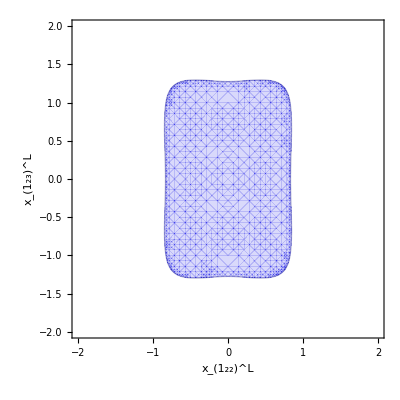

```mathematica
pltLFC=ContourPlot[χ2["LFC"][x22,x23]-min["LFC"],
{x22,-2,2},
{x23,-2,2},
Contours->{N2σ,10^20},
ContourShading->{Opacity[0.15,Darker[Blue,0.1]],Transparent},
ContourStyle->{Directive[Opacity[0.3,Darker[Blue,0.55]]],Transparent},
FrameLabel->{
Coupling["x1L",{2,2}]//TraditionalForm,
Coupling["x1L",{2,3}]//TraditionalForm
}
]
```

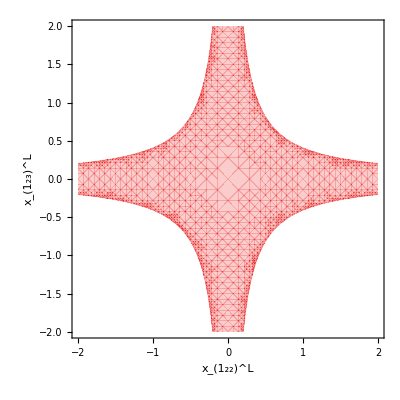

```mathematica
pltμτ=ContourPlot[χ2["μτ"][x22,x23]-min["μτ"],
{x22,-2,2},
{x23,-2,2},
Contours->{N2σ,10^20},
ContourShading->{Opacity[0.2,Darker[Red,0.1]],Transparent},
ContourStyle->{Opacity[0.2,Darker[Red,0.1]],Transparent},
FrameLabel->{
Coupling["x1L",{2,2}]//TraditionalForm,
Coupling["x1L",{2,3}]//TraditionalForm
}
]
```

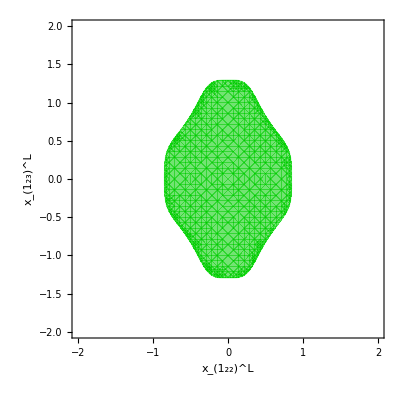

```mathematica
pltfull=ContourPlot[χ2["full"][x22,x23]-min["full"],
{x22,-2,2},
{x23,-2,2},
Contours->{N2σ,10^20},
ContourShading->{Opacity[0.55,Darker[Green,0.2]],Transparent},
ContourStyle->{Directive[Opacity[0.3,Darker[Green,0.1]]],Transparent},
FrameLabel->{
Coupling["x1L",{2,2}]//TraditionalForm,
Coupling["x1L",{2,3}]//TraditionalForm
}
]
```

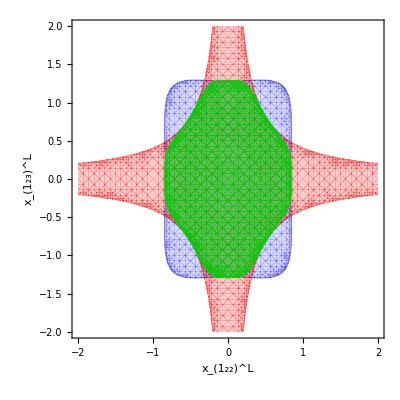

```mathematica
pltcombined=Show[{pltLFC,pltμτ,pltfull}]
```